# Analysis of Packing V3E06L0N02T1_1

Three Vertices, Six Edges, 0 Loops,Combinatorial Number 02, Face Pattern 1, Type 1

```mathematica
-Graphics-;
```

This packing is fairly straight forward; we just use the fact that 2 lies on the perpendicular bisector of w2 and w1, and similarly for 3.  For 3, also notice that the angle between w1, (0,0), and the edge to 3 is -α.   Also, 2 and 3 must be small circles, because of the number of tangencies.  Below, (x2b,y2b) corresponds to the center of a small circle, circle 2; (x3b,y3b) corresponds to the center of a small circle, circle 3.  Also, we scale the picture so that the radius of the big circle is 1/2, so the distance of rb+rs= (1/Sqrt[2]).

```mathematica
x2b:=(1/Sqrt[2])*Cos[α]
```

```mathematica
y2b:=(1/Sqrt[2])*Sin[α]
```

```mathematica
x3b:=(1/Sqrt[2])*Cos[-α]+((2/Sqrt[2])(Cos[β]))*Cos[β+α]
```

```mathematica
y3b:=(1/Sqrt[2])*Sin[-α]+((2/Sqrt[2])(Cos[β]))*Sin[β+α]
```

## Circle Centers and Radii

```mathematica
centers = {{0,0},{(1/Sqrt[2])*Cos[α],(1/Sqrt[2])*Sin[α]},{(1/Sqrt[2])*Cos[-α]+((2/Sqrt[2])(Cos[β]))*Cos[β+α],(1/Sqrt[2])*Sin[-α]+((2/Sqrt[2])(Cos[β]))*Sin[β+α]}}
```

{{0,0},{Cos[α]/(√2),Sin[α]/(√2)},{Cos[α]/(√2)+√2 Cos[β] Cos[α+β],-Sin[α]/(√2)+√2 Cos[β] Sin[α+β]}}

## Lattice Vectors

We are working this flat torus

```mathematica
latticeVectors = {
 {(2/Sqrt[2])*Cos[α],0},
{ ((2 /√2 )*Cos[β] )*Cos[α+β],((2 /√2 )*Cos[β] )*Sin[α+β]}};
```

Notice that the length of the vector along the diagonal from vector w1 to vector w2 must be larger than 1 (the diameter of the big circle) otherwise the two big circles centered t	here overlap

```mathematica
blah:=Simplify[latticeVectors[[1]]-latticeVectors[[2]]]
```

```mathematica
αβRelation := Simplify[blah[[1]]^2+blah[[2]]^2]
αβRelation
```

2 Sin[α+β]^2

So 2 Sin[α+β]^2>1

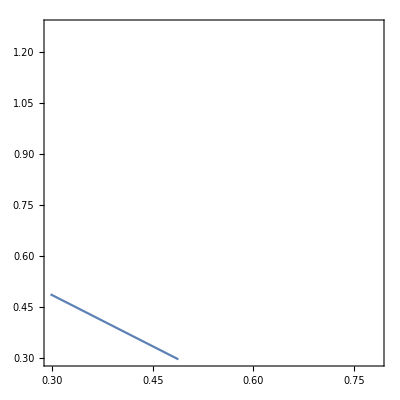

```mathematica
ContourPlot[αβRelation==1,{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])}]
```

Need to exclude above the blue line.

Also, the length of w2 must be bigger than one:

```mathematica
Simplify[Sqrt[(((2 /√2 )*Cos[β] )*Cos[α+β])^2+(((2 /√2 )*Cos[β] )*Sin[α+β])^2]]
```

√(1+Cos[2 β])

So √(1+Cos[2 β])>1

Finally, in order to prevent duplication of packings, we want the slope of the segment from circle 3 to the endpoint of w1 to be positive, so that we don’t duplicate any packings.

```mathematica
slopeC3W1:=(centers[[3]][[2]]-latticeVectors[[1]][[2]])/(centers[[3]][[1]]-latticeVectors[[1]][[1]])
Simplify[slopeC3W1]
```

Tan[α+2 β]

So, Tan[α+2 β]>0

## Edges

Here we store the edges a list {i,j,m,n} where center[[i]] is connected to center[[j]] + m*latticeVectors[[1]] + n*latticeVectors[2]]
center[[i]] is *always* in the fundamental domain ****the last two numbers are winding numbers****

```mathematica
edges = {{1,2,0,0},{2,1,0,1},{2,1,1,0},{3,1,0,1},{3,1,1,1},{3,1,1,0}};
```

### Check the edge lengths are all 2rs= Sqrt[2]-1 or rs+rb=Sqrt[2]rb=Sqrt[2]/2=1/Sqrt[2]

```mathematica
For[i=1,i≤Length[edges],i++,
P1:= centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]];
P2:= centers[[edges[[i,1]] ]];
Print["Edge ",i,": Length is ",
Sqrt[FullSimplify[(P1[[1]]-P2[[1]])^2+(P1[[2]]-P2[[2]])^2,{0≤α≤ Pi/2,0≤β≤ Pi/2}]]];
]
```

Edge 1: Length is 1/(√2)

Edge 2: Length is 1/(√2)

Edge 3: Length is 1/(√2)

Edge 4: Length is 1/(√2)

Edge 5: Length is 1/(√2)

Edge 6: Length is 1/(√2)

Yes!

## Packing Visualization

Here we visualize the packing and the fundamental domain to help determine the value of the parameters for which this is a packing graph.

```mathematica
Manipulate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[1]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[1]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,Pi/4,"α"},ArcSin[1-1/(√2)],Pi/4},{{b,Pi/4,"β"},ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-a}]
```

I tried restricting the plot window for β to 1/2 of what it is now,  but with no luck.  Below is the work.

```mathematica
Simplify[((1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-a)-ArcSin[1-1/(√2)])/2]
```

1/4 (-2 a+π-2 (ArcSin[1-1/(√2)]+ArcTan[(-1+√2)/(√(-1+2 √2))]))

```mathematica
Simplify[ArcSin[1-1/(√2)]+(1/4 (-2 a+π-2 (ArcSin[1-1/(√2)]+ArcTan[(-1+√2)/(√(-1+2 √2))])))]
```

1/4 (-2 a+π+2 ArcSin[1-1/(√2)]-2 ArcTan[(-1+√2)/(√(-1+2 √2))])

## Locally Maximally Dense

We have to determine for which values of α and β the packing is locally maximally dense. To be locally maximally dense (Following Connelly, Rigid Circle and Sphere Packings, Page 51, Theorem 6.1)
	1. The packing graph is rigid as a bar framework
	2. Have a proper stress that is non-zero on every member

### Rigid as bar framework

To be rigid as a bar framework we need to establish a rigid ordering of the circles. The numbering of the circles in the picture above is a rigid ordering of the packing disks -- See Lemma 6.2 in the Connelly paper on Rigid Sphere and Circle Packings. Note: The first is held fixed.

### Proper Stress

Assign a scalar to each edge of the packing and collect those scalars in a vector called ω. We need to solve the linear algebra problem where the sum of the ω_i times the vector from vertex j is zero.

```mathematica
Manipulate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}},(*Angle Markers Labels*)
Table[Text[Style[Subscript["ω",i],Large,Red],1/2*(centers[[edges[[i,1]] ]]+centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]])/.{α->a,β->b}],{i,1,Length[edges]}](*Label Edges With Stresses*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,Pi/4,"α"},ArcSin[1-1/(√2)],Pi/4},{{b,Pi/4,"β"},ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-a}
]
```

```mathematica
equations = Table[{0,0},{k,Length[centers]}]; (*Start with the zero equations*)
w =Table[Subscript[ω,i],{i,Length[edges]}]; (*Initialize a vector of Subscript[ω, i]*)
For[i=1,i≤Length[centers], i++, (*i is the center number*)
For[j=1,j≤Length[edges], j++, (*j is the edge number*)
If[edges[[j,1]]==i, (*center i is the starting point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(centers[[edges[[j,1]] ]]-centers[[edges[[j,2]] ]]-
edges[[j,3]]*latticeVectors[[1]]-
edges[[j,4]]*latticeVectors[[2]])] 
If[edges[[j,2]]==i, (*center i is the ending point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(-centers[[edges[[j,1]] ]]+centers[[edges[[j,2]] ]]+
edges[[j,3]]*latticeVectors[[1]]+
edges[[j,4]]*latticeVectors[[2]])]
]
]
stresses = Flatten[Simplify[Solve[Flatten[equations]==Flatten[Table[{0,0},{k,Length[centers]}]],w]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ω_2→Csc[2 (α+β)] Sin[2 α] ω_1,ω_3→Csc[2 (α+β)] Sin[2 β] ω_1,ω_4→Cos[β] Csc[α] Sec[α] Sin[β] ω_6,ω_5→Csc[2 α] Sin[2 (α+β)] ω_6}

Notice that stress ω_1, ω_6 is free.

```mathematica
yuck := Simplify[equations /. stresses] (*check the solutions, Should output all zeros but I don't think Mathematica can simplify it*)
```

```mathematica
N[Simplify[yuck/.{α-> 5Pi/6,β-> 5Pi/6}]]
```

{{0.,0.},{0.,0.},{0.,0.}}

```mathematica
guts := Simplify[Union[{0},Table[Subscript[ω, i]/.stresses,(*first list all of the right hand sides of all the stresses*)
{i,Length[edges]}]/.{Subscript[ω, 1]->.5,Subscript[ω, 6]->.5}]]
```

```mathematica
Plot3D[guts,{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α},RegionFunction->Function[{α,β},Tan[α+2 β]>0  ],AxesLabel->Automatic]
```

-Graphics3D-

So all stresses are positive.

## Moduli Space Of Locally Maximally Dense Packings

Determine the Torus Angle and Ratio for the packings that are locally maximally dense.

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{α,β},Reals],ArcSin[1-1/(√2)]<α<Pi/4,ArcSin[1-1/(√2)]<β<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,√(1+Cos[2 β])>1,2 Sin[α+β]^2>1,Tan[α+2 β]>0}]
```

α+β

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[2]]]/EuclideanDistance[{0,0},latticeVectors[[1]]],{Element[{α,β},Reals],ArcSin[1-1/(√2)]<α<Pi/4,ArcSin[1-1/(√2)]<β<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,√(1+Cos[2 β])>1,2 Sin[α+β]^2>1,Tan[α+2 β]>0}]
```

Cos[β] Sec[α]

Now plot the region of the moduli space that is covered by (r,theta)=(torusRatio,torusAngle). The right boundary is in the region, the others are not.

First when we plot we get:

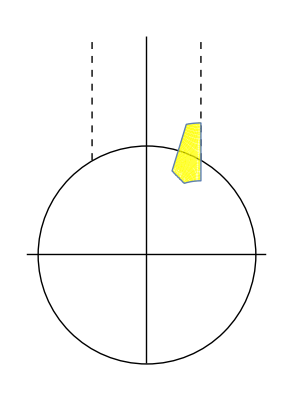

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α},RegionFunction->(  2 Sin[#3+#4]^2>1 && √(1+Cos[2 #4])>1&& Tan[#3+2 #4]<0&),PlotStyle->Yellow]]
```

Then, to flip the picture up, we look when the torus ratio is less than one and when the torus ratio is less than one, we take the recpirocal of the torus ratio.

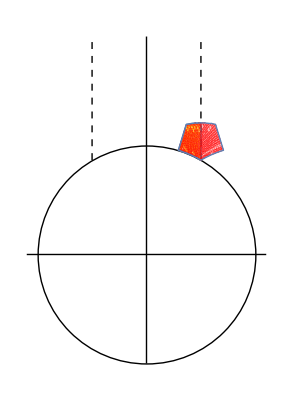

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α},RegionFunction->(  2 Sin[#3+#4]^2>1 && √(1+Cos[2 #4])>1&& Tan[#3+2 #4]<0&& Cos[#4] Sec[#3]>1&), PlotStyle->Yellow]
,ParametricPlot[{Re[((1/torusRatio)*Exp[I torusAngleFromVectors])],Im[((1/torusRatio)*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α},RegionFunction->(  2 Sin[#3+#4]^2>1 && √(1+Cos[2 #4])>1&& Tan[#3+2 #4]<0&& Cos[#4] Sec[#3]<1&),PlotStyle->Red]

]
```

However, notice that this overlaps with the yellow region.  Because each locally maximally dense packing can only correspond to one embedding, and the red region overlaps with the yellow region, we don’t need to consider the red region.

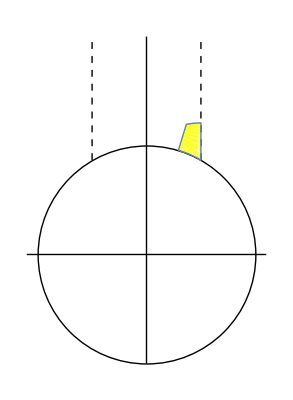

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α},RegionFunction->(  2 Sin[#3+#4]^2>1 && √(1+Cos[2 #4])>1&& Tan[#3+2 #4]<0&& Cos[#4] Sec[#3]>1&), PlotStyle->Yellow]
(*because every embedding can only correspond to one unqiue locally maximally dense packing, we can get rid of this plot ParametricPlot[{Re[((1/torusRatio)*Exp[I torusAngleFromVectors])],Im[((1/torusRatio)*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α},RegionFunction->(  2 Sin[#3+#4]^2>1 && √(1+Cos[2 #4])>1&& Tan[#3+2 #4]<0&& Cos[#4] Sec[#3]<1&),PlotStyle->Red],*)

]
```

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{α,β},Reals],ArcSin[1-1/(√2)]<α<Pi/4,ArcSin[1-1/(√2)]<β<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,√(1+Cos[2 β])>1,2 Sin[α+β]^2>1,Tan[α+2 β]>0}]
```

1/8 (7-4 √2) π Csc[α+β] Sec[α] Sec[β]

Plot the density over the parameter space

```mathematica
Plot3D[torusDensity,{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α},RegionFunction->(  2 Sin[#3+#4]^2>1 && √(1+Cos[2 #4])>1&& Tan[#3+2 #4]<0&),AxesLabel->Automatic]
```

Plot3D::invregion: (2 Sin[Plus[«2»]]^2>1&&√(1+Cos[Times[«2»]])>1&&Tan[#3+2 Slot[«1»]]<0&)[Identity[#1],Identity[#2],Identity[#3]]& must be a Boolean function.

-Graphics3D-

Color the moduli space region with color depending on the density. Red shade is close to 1 and Blue shade is close to .5

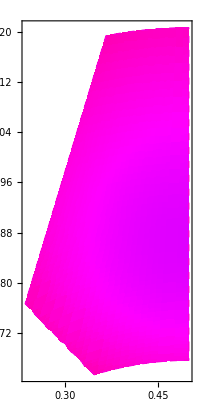

```mathematica
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α},RegionFunction->(  2 Sin[#3+#4]^2>1 && √(1+Cos[2 #4])>1&& Tan[#3+2 #4]<0&),ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
```

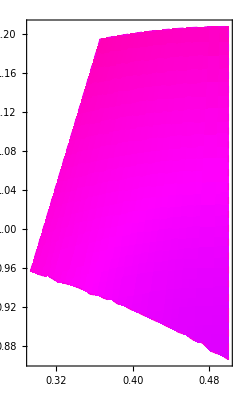

```mathematica
Show[
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α},RegionFunction->(  2 Sin[#3+#4]^2>1 && √(1+Cos[2 #4])>1&& Tan[#3+2 #4]<0&&Cos[#4] Sec[#3]>1&),ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None] 
]
```

Now find the minimum density with in the region.

```mathematica
NMinimize[{torusDensity,ArcSin[1-1/(√2)]<α &&α<Pi/4&& ArcSin[1-1/(√2)]<β&& β<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α && √(1+Cos[2 β])>1 && 2 Sin[α+β]^2>1 && Tan[α+2 β]>0 },{{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.8120656361148707300911073050334355308134,{α→0.5235987752981407276350068708851807155024,β→0.5235987754723018873986531838808579674177}}